```mathematica
Nt = 20(*647*); 
ti = 0; tf = 5; 
deltat = (tf - ti) /Nt ;
Nx = 20(*455*);
xi = -40; xf = 40; 
deltax = (xf - xi) / Nx; 
c =  1;

(*For Max Eigenvalue Plots*)
rs = Table[0.1*i,{i,1,200}];

maxevalsLD2 = Table[0,{i,1,Length[rs]}];
maxevalsRK2 = Table[0,{i,1,Length[rs]}];
maxevalsPI = Table[0,{i,1,Length[rs]}];



Subscript[δ, i_,j_]:=KroneckerDelta[i,j];

selectwidth = 8;
diffOrder = 2;
deriv = 2;


(*The total number of points in the stencil*)
totalpoints = (2*selectwidth) + 1;

(*The middle point in the stencil*)
middlepoint = selectwidth + 1;

(*Set up the grid for the stencil*)
grid=x0+(Range[totalpoints]-middlepoint)Δx;

(LP=NDSolve`FiniteDifferenceDerivative[Derivative[deriv],grid,"DifferenceOrder"->diffOrder]@"DifferentiationMatrix"//Normal);

(*define r:=Δt/(Δx^deriv)*)
r=.;
LPX = LP*((-1)^deriv)*(r*(Δx)^deriv);

gn = (LPX[[middlepoint,All]]//Normal)//Simplify//FullSimplify;
LPX = Table[RotateRight[gn,i],{i,-selectwidth,selectwidth}];
LPX[[1,-1]]=0;
LPX[[1,-2]]=0;
LPX[[2,-1]]=0;
LPX[[-1,1]]=0;
LPX[[-1,2]]=0;
LPX[[-2,1]]=0;
LPX[[-3,1]] = 0;
LPX[[-2,2]] = 0;
LPX[[-1,3]] = 0;
LPX[[1,-3]] = 0;
LPX[[2,-2]] = 0;
LPX[[3,-1]] = 0;

IP=IdentityMatrix[Length[LPX]];

(Mn=Inverse[IP-(ⅈ * LPX)/4 ].(IP+(ⅈ * LPX)/4));

fn=(Mn[[middlepoint,All]]//Normal)//Simplify//FullSimplify;
```

```mathematica
Do[
deltat = (deltax^2) * rs[[p]];

Xp= N[Table[xm = xi + m *deltax, {m, 0, Nx}],32];

T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1 }],32];
Xo = N[Table[xn = xi + n *deltax, {n, 0, Nx -1}],32];

f[x_] = ⅇ^(- x^2+ⅈ x);


(************************************************************************************************************************)
(*Differentiation Matrix*)
(************************************************************************************************************************)
L1 = N[(NDSolve`FiniteDifferenceDerivative[Derivative[1],Xp,"DifferenceOrder"->1, PeriodicInterpolation->True]@"DifferentiationMatrix"//Normal),32];
L1//MatrixForm;
DL1 = N[-c * L1 * deltat,32];
DL1[[1,-1]]=0;
DL1[[1,-2]]=0;
DL1[[2,-1]]=0;
DL1[[-1,1]]=0;
DL1[[-1,2]]=0;
DL1[[-2,1]]=0;
DL1[[-3,1]] = 0;
DL1[[-2,2]] = 0;
DL1[[-1,3]] = 0;
DL1[[1,-3]] = 0;
DL1[[2,-2]] = 0;
DL1[[3,-1]] = 0;


L2 = N[Table[(NDSolve`FiniteDifferenceDerivative[Derivative[i],Xp, "DifferenceOrder"->2, PeriodicInterpolation->True]@"DifferentiationMatrix"//Normal), {i,1,8}],32];
DL2 = L2[[2]] * deltat * (ⅈ / 2);
DL2[[1,-1]]=0;
DL2[[1,-2]]=0;
DL2[[2,-1]]=0;
DL2[[-1,1]]=0;
DL2[[-1,2]]=0;
DL2[[-2,1]]=0;
DL2[[-3,1]] = 0;
DL2[[-2,2]] = 0;
DL2[[-1,3]] = 0;
DL2[[1,-3]] = 0;
DL2[[2,-2]] = 0;
DL2[[3,-1]] = 0;



(* LD2 *)
ILD2 = N[IdentityMatrix[Length[DL2]],32];
ALD2 = N[ILD2 - (DL2 / 2),32];
BLD2 = N[ILD2 + (DL2 / 2),32];
MLD2 = N[Inverse[ALD2].BLD2,32];

evals = Eigenvalues[N[MLD2]];

maxevalsLD2[[p]] = Max[Abs[evals]];

(*PI*)
(*Generate a M Matrix from the L matrix for the stencil*)
MP = Table[0,{i,1,Nx},{j,1,Nx}];

fn = N[fn//.{r -> (deltat / (deltax)^deriv)},32];

(*WITHOUT Periodic Boundary Conditions Placed*)
MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]],{i,0,Nx},{j,0,Nx}];

(*WITH Periodic Boundary Conditions*)
(*MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]] + Sum[(Subscript[δ, (i + Nx) - n,j])fn[[selectwidth - n]] + (Subscript[δ, (i + Nx) + n,(j + 2*Nx)])fn[[(middlepoint + 1) + n]]  ,{n,0,selectwidth - 1}],{i,0,Nx-1},{j,0,Nx-1}];*)


evalsPI = Eigenvalues[N[MP]];

maxevalsPI[[p]] = Max[Abs[evalsPI]];

Print["Finished "<>ToString[rs[[p]]]];


,{p,1,Length[rs]}]


(*For Max Eigenvalue Plots*)
(*exportData=Flatten/@Transpose[{rsLD2,maxevalsLD2,rsEuler, maxevalsEuler, rsRK2, maxevalsRK2, rsRK4, maxevalsRK4, rsN, maxevalsN}];*)
(*Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\evals_max.dat",exportData,"Table"];*)
```

Finished 0.1

Finished 0.2

Finished 0.3

Finished 0.4

Finished 0.5

Finished 0.6

Finished 0.7

Finished 0.8

Finished 0.9

Finished 1.

Finished 1.1

Finished 1.2

Finished 1.3

Finished 1.4

Finished 1.5

Finished 1.6

Finished 1.7

Finished 1.8

Finished 1.9

Finished 2.

Finished 2.1

Finished 2.2

Finished 2.3

Finished 2.4

Finished 2.5

Finished 2.6

Finished 2.7

Finished 2.8

Finished 2.9

Finished 3.

Finished 3.1

Finished 3.2

Finished 3.3

Finished 3.4

Finished 3.5

Finished 3.6

Finished 3.7

Finished 3.8

Finished 3.9

Finished 4.

Finished 4.1

Finished 4.2

Finished 4.3

Finished 4.4

Finished 4.5

Finished 4.6

Finished 4.7

Finished 4.8

Finished 4.9

Finished 5.

Finished 5.1

Finished 5.2

Finished 5.3

Finished 5.4

Finished 5.5

Finished 5.6

Finished 5.7

Finished 5.8

Finished 5.9

Finished 6.

Finished 6.1

Finished 6.2

Finished 6.3

Finished 6.4

Finished 6.5

Finished 6.6

Finished 6.7

Finished 6.8

Finished 6.9

Finished 7.

Finished 7.1

Finished 7.2

Finished 7.3

Finished 7.4

Finished 7.5

Finished 7.6

Finished 7.7

Finished 7.8

Finished 7.9

Finished 8.

Finished 8.1

Finished 8.2

Finished 8.3

Finished 8.4

Finished 8.5

Finished 8.6

Finished 8.7

Finished 8.8

Finished 8.9

Finished 9.

Finished 9.1

Finished 9.2

Finished 9.3

Finished 9.4

Finished 9.5

Finished 9.6

Finished 9.7

Finished 9.8

Finished 9.9

Finished 10.

Finished 10.1

Finished 10.2

Finished 10.3

Finished 10.4

Finished 10.5

Finished 10.6

Finished 10.7

Finished 10.8

Finished 10.9

Finished 11.

Finished 11.1

Finished 11.2

Finished 11.3

Finished 11.4

Finished 11.5

Finished 11.6

Finished 11.7

Finished 11.8

Finished 11.9

Finished 12.

Finished 12.1

Finished 12.2

Finished 12.3

Finished 12.4

Finished 12.5

Finished 12.6

Finished 12.7

Finished 12.8

Finished 12.9

Finished 13.

Finished 13.1

Finished 13.2

Finished 13.3

Finished 13.4

Finished 13.5

Finished 13.6

Finished 13.7

Finished 13.8

Finished 13.9

Finished 14.

Finished 14.1

Finished 14.2

Finished 14.3

Finished 14.4

Finished 14.5

Finished 14.6

Finished 14.7

Finished 14.8

Finished 14.9

Finished 15.

Finished 15.1

Finished 15.2

Finished 15.3

Finished 15.4

Finished 15.5

Finished 15.6

Finished 15.7

Finished 15.8

Finished 15.9

Finished 16.

Finished 16.1

Finished 16.2

Finished 16.3

Finished 16.4

Finished 16.5

Finished 16.6

Finished 16.7

Finished 16.8

Finished 16.9

Finished 17.

Finished 17.1

Finished 17.2

Finished 17.3

Finished 17.4

Finished 17.5

Finished 17.6

Finished 17.7

Finished 17.8

Finished 17.9

Finished 18.

Finished 18.1

Finished 18.2

Finished 18.3

Finished 18.4

Finished 18.5

Finished 18.6

Finished 18.7

Finished 18.8

Finished 18.9

Finished 19.

Finished 19.1

Finished 19.2

Finished 19.3

Finished 19.4

Finished 19.5

Finished 19.6

Finished 19.7

Finished 19.8

Finished 19.9

Finished 20.

```mathematica
maxevalsLD2 = Join[{1},maxevalsLD2];
rsLD2 = Join[{0},rs];

maxevalsPI = Join[{1},maxevalsPI];
rsPI = Join[{0},rs];
```

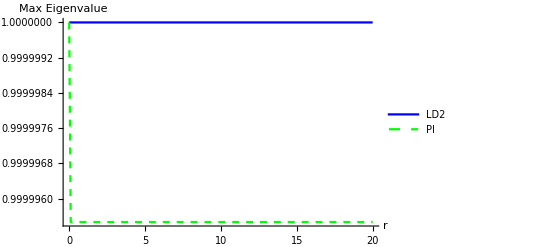

```mathematica
ListLinePlot[{Transpose[{rsLD2,maxevalsLD2}],Transpose[{rsPI,maxevalsPI}]},PlotStyle->{Blue, {Green, Dashed}}, PlotLegends->{"LD2", "PI"}, AxesLabel->{"r", "Max Eigenvalue"}]
```

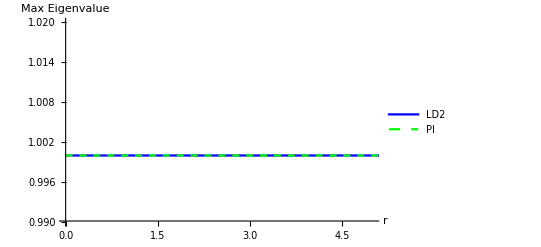

```mathematica
ListLinePlot[{Transpose[{rsLD2,maxevalsLD2}],Transpose[{rsPI,maxevalsPI}]},PlotStyle->{Blue, {Green, Dashed}}, PlotLegends->{"LD2", "PI"},PlotRange->{{0,5},{.99,1.02}}, AxesLabel->{"r", "Max Eigenvalue"}]
```

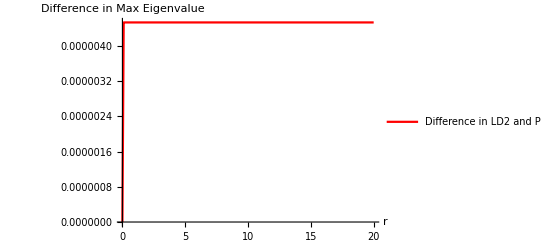

```mathematica
ListLinePlot[{Transpose[{rsLD2,Abs[maxevalsLD2 - maxevalsPI]}]},PlotStyle->{Red}, PlotLegends->{"Difference in LD2 and PI"}, AxesLabel->{"r", "Difference in Max Eigenvalue"}]
```

```mathematica
Abs[maxevalsLD2 - maxevalsPI]
```

{0,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6,4.53209×10^-6}

```mathematica
MP//MatrixForm
```

(0.992554-0.0993799 ⅈ | 0.00495663+0.0495353 ⅈ | -0.00122836+0.00018518 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.00495663+0.0495353 ⅈ | 0.992554-0.0993799 ⅈ | 0.00495663+0.0495353 ⅈ | -0.00122836+0.00018518 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-0.00122836+0.00018518 ⅈ | 0.00495663+0.0495353 ⅈ | 0.992554-0.0993799 ⅈ | 0.00495663+0.0495353 ⅈ | -0.00122836+0.00018518 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-6.1439×10^-6-0.0000303832 ⅈ | -0.00122836+0.00018518 ⅈ | 0.00495663+0.0495353 ⅈ | 0.992554-0.0993799 ⅈ | 0.00495663+0.0495353 ⅈ | -0.00122836+0.00018518 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
7.49572×10^-7-1.90934×10^-7 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | -0.00122836+0.00018518 ⅈ | 0.00495663+0.0495353 ⅈ | 0.992554-0.0993799 ⅈ | 0.00495663+0.0495353 ⅈ | -0.00122836+0.00018518 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
5.69139×10^-9+1.84434×10^-8 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | -0.00122836+0.00018518 ⅈ | 0.00495663+0.0495353 ⅈ | 0.992554-0.0993799 ⅈ | 0.00495663+0.0495353 ⅈ | -0.00122836+0.00018518 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-4.52568×10^-10+1.64796×10^-10 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | -0.00122836+0.00018518 ⅈ | 0.00495663+0.0495353 ⅈ | 0.992554-0.0993799 ⅈ | 0.00495663+0.0495353 ⅈ | -0.00122836+0.00018518 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-4.67035×10^-12-1.10739×10^-11 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | -0.00122836+0.00018518 ⅈ | 0.00495663+0.0495353 ⅈ | 0.992554-0.0993799 ⅈ | 0.00495663+0.0495353 ⅈ | -0.00122836+0.00018518 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
2.70335×10^-13-1.30276×10^-13 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | -0.00122836+0.00018518 ⅈ | 0.00495663+0.0495353 ⅈ | 0.992554-0.0993799 ⅈ | 0.00495663+0.0495353 ⅈ | -0.00122836+0.00018518 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | -0.00122836+0.00018518 ⅈ | 0.00495663+0.0495353 ⅈ | 0.992554-0.0993799 ⅈ | 0.00495663+0.0495353 ⅈ | -0.00122836+0.00018518 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | -0.00122836+0.00018518 ⅈ | 0.00495663+0.0495353 ⅈ | 0.992554-0.0993799 ⅈ | 0.00495663+0.0495353 ⅈ | -0.00122836+0.00018518 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | -0.00122836+0.00018518 ⅈ | 0.00495663+0.0495353 ⅈ | 0.992554-0.0993799 ⅈ | 0.00495663+0.0495353 ⅈ | -0.00122836+0.00018518 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | -0.00122836+0.00018518 ⅈ | 0.00495663+0.0495353 ⅈ | 0.992554-0.0993799 ⅈ | 0.00495663+0.0495353 ⅈ | -0.00122836+0.00018518 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | -0.00122836+0.00018518 ⅈ | 0.00495663+0.0495353 ⅈ | 0.992554-0.0993799 ⅈ | 0.00495663+0.0495353 ⅈ | -0.00122836+0.00018518 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | -0.00122836+0.00018518 ⅈ | 0.00495663+0.0495353 ⅈ | 0.992554-0.0993799 ⅈ | 0.00495663+0.0495353 ⅈ | -0.00122836+0.00018518 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | -0.00122836+0.00018518 ⅈ | 0.00495663+0.0495353 ⅈ | 0.992554-0.0993799 ⅈ | 0.00495663+0.0495353 ⅈ | -0.00122836+0.00018518 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | -0.00122836+0.00018518 ⅈ | 0.00495663+0.0495353 ⅈ | 0.992554-0.0993799 ⅈ | 0.00495663+0.0495353 ⅈ | -0.00122836+0.00018518 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | -0.00122836+0.00018518 ⅈ | 0.00495663+0.0495353 ⅈ | 0.992554-0.0993799 ⅈ | 0.00495663+0.0495353 ⅈ | -0.00122836+0.00018518 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | -0.00122836+0.00018518 ⅈ | 0.00495663+0.0495353 ⅈ | 0.992554-0.0993799 ⅈ | 0.00495663+0.0495353 ⅈ | -0.00122836+0.00018518 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | -0.00122836+0.00018518 ⅈ | 0.00495663+0.0495353 ⅈ | 0.992554-0.0993799 ⅈ | 0.00495663+0.0495353 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 2.70335×10^-13-1.30276×10^-13 ⅈ | -4.67035×10^-12-1.10739×10^-11 ⅈ | -4.52568×10^-10+1.64796×10^-10 ⅈ | 5.69139×10^-9+1.84434×10^-8 ⅈ | 7.49572×10^-7-1.90934×10^-7 ⅈ | -6.1439×10^-6-0.0000303832 ⅈ | -0.00122836+0.00018518 ⅈ | 0.00495663+0.0495353 ⅈ | 0.992554-0.0993799 ⅈ)

```mathematica
DL2[[-1, All]]
```

{0,0,0,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+10. ⅈ,0.-20. ⅈ}